### Start choosing the example:

```mathematica
t=27;
beta = 0;
A = 0.2;
(*I1=2,U1=5*)
```

### DataToEquations and the critical congestion solver

```mathematica
Data=DataG[t]
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,80}},Exit Vertices and Terminal Costs→{{10,15}},Switching Costs→{}|>

```mathematica
Data["Entrance Vertices and Currents"]={{1,1}};
Data["Exit Vertices and Terminal Costs"]={{10,1000}};
```

```mathematica
MFGEquations=DataToEquations[Data];//Timing
```

DataToEquations: Finished assembling strucural equations. Reducing the structural system ...

DataToEquations: Critical case ...

DataToEquations: Critical congestion solved.

DataToEquations: Done.

{0.028458,Null}

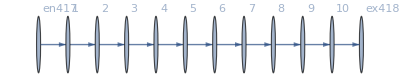

```mathematica
MFGEquations["FG"]
```

```mathematica
MFGEquations["criticalreduced1"][[2]]//KeySort
```

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1009.,u462→1008.,u463→1007.,u464→1006.,u465→1005.,u466→1004.,u467→1003.,u468→1002.,u469→1001.,u470→1000,u471→1009.,u472→-1+1009.,u473→-1+1008.,u474→-1+1007.,u475→-1+1006.,u476→-1+1005.,u477→-1+1004.,u478→-1+1003.,u479→-1+1002.,u480→-1+1001.,u481→1000,u482→1009.|>

```mathematica
Data
```

<|Vertices List→{1,2,3,4,5,6,7,8,9,10},Adjacency Matrix→{{0,1,0,0,0,0,0,0,0,0},{0,0,1,0,0,0,0,0,0,0},{0,0,0,1,0,0,0,0,0,0},{0,0,0,0,1,0,0,0,0,0},{0,0,0,0,0,1,0,0,0,0},{0,0,0,0,0,0,1,0,0,0},{0,0,0,0,0,0,0,1,0,0},{0,0,0,0,0,0,0,0,1,0},{0,0,0,0,0,0,0,0,0,1},{0,0,0,0,0,0,0,0,0,0}},Entrance Vertices and Currents→{{1,1}},Exit Vertices and Terminal Costs→{{10,1000}},Switching Costs→{}|>

#### Non-linear case

```mathematica
alpha = 0;
FFR= FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.87618×10^-13

FRX1: The Error on the nonlinear terms is 2.87618×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1006.35,u462→1005.65,u463→1004.94,u464→1004.23,u465→1003.53,u466→1002.82,u467→1002.12,u468→1001.41,u469→1000.71,u470→1000,u471→0.+1. 1006.35,u472→0.+1. 1005.65,u473→0.+1. 1004.94,u474→0.+1. 1004.23,u475→0.+1. 1003.53,u476→0.+1. 1002.82,u477→0.+1. 1002.12,u478→0.+1. 1001.41,u479→0.+1. 1000.71,u480→1000.,u481→1000,u482→0.+1. 1006.35|>

```mathematica
alpha = 0.1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 5.31295×10^-13

FRX1: The Error on the nonlinear terms is 5.31295×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1006.54,u462→1005.81,u463→1005.09,u464→1004.36,u465→1003.63,u466→1002.91,u467→1002.18,u468→1001.45,u469→1000.73,u470→1000,u471→0.+1. 1006.54,u472→0.+1. 1005.81,u473→0.+1. 1005.09,u474→0.+1. 1004.36,u475→0.+1. 1003.63,u476→0.+1. 1002.91,u477→0.+1. 1002.18,u478→0.+1. 1001.45,u479→0.+1. 1000.73,u480→1000.,u481→1000,u482→0.+1. 1006.54|>

```mathematica
alpha = 0.3;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.08428×10^-13

FRX1: The Error on the nonlinear terms is 4.08428×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1006.96,u462→1006.19,u463→1005.41,u464→1004.64,u465→1003.87,u466→1003.09,u467→1002.32,u468→1001.55,u469→1000.77,u470→1000,u471→0.+1. 1006.96,u472→0.+1. 1006.19,u473→0.+1. 1005.41,u474→0.+1. 1004.64,u475→0.+1. 1003.87,u476→0.+1. 1003.09,u477→0.+1. 1002.32,u478→0.+1. 1001.55,u479→0.+1. 1000.77,u480→1000.,u481→1000,u482→0.+1. 1006.96|>

```mathematica
alpha = 0.9;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.91827×10^-13

FRX1: The Error on the nonlinear terms is 2.91827×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1008.63,u462→1007.67,u463→1006.71,u464→1005.76,u465→1004.8,u466→1003.84,u467→1002.88,u468→1001.92,u469→1000.96,u470→1000,u471→0.+1. 1008.63,u472→0.+1. 1007.67,u473→0.+1. 1006.71,u474→0.+1. 1005.76,u475→0.+1. 1004.8,u476→0.+1. 1003.84,u477→0.+1. 1002.88,u478→0.+1. 1001.92,u479→0.+1. 1000.96,u480→1000.,u481→1000,u482→0.+1. 1008.63|>

```mathematica
alpha = 1;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 3.33067×10^-15

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1009.,u462→1008.,u463→1007.,u464→1006.,u465→1005.,u466→1004.,u467→1003.,u468→1002.,u469→1001.,u470→1000,u471→0.+1. 1009.,u472→0.+1. 1008.,u473→0.+1. 1007.,u474→0.+1. 1006.,u475→0.+1. 1005.,u476→0.+1. 1004.,u477→0.+1. 1003.,u478→0.+1. 1002.,u479→0.+1. 1001.,u480→1000.,u481→1000,u482→0.+1. 1009.|>

```mathematica
alpha = 1.2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.10525×10^-13

FRX1: The Error on the nonlinear terms is 4.10525×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1009.85,u462→1008.75,u463→1007.66,u464→1006.56,u465→1005.47,u466→1004.38,u467→1003.28,u468→1002.19,u469→1001.09,u470→1000,u471→0.+1. 1009.85,u472→0.+1. 1008.75,u473→0.+1. 1007.66,u474→0.+1. 1006.56,u475→0.+1. 1005.47,u476→0.+1. 1004.38,u477→0.+1. 1003.28,u478→0.+1. 1002.19,u479→0.+1. 1001.09,u480→1000.,u481→1000,u482→0.+1. 1009.85|>

```mathematica
alpha = 1.5;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.93465×10^-13

FRX1: The Error on the nonlinear terms is 2.93465×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1011.51,u462→1010.23,u463→1008.95,u464→1007.67,u465→1006.39,u466→1005.12,u467→1003.84,u468→1002.56,u469→1001.28,u470→1000,u471→0.+1. 1011.51,u472→0.+1. 1010.23,u473→0.+1. 1008.95,u474→0.+1. 1007.67,u475→0.+1. 1006.39,u476→0.+1. 1005.12,u477→0.+1. 1003.84,u478→0.+1. 1002.56,u479→0.+1. 1001.28,u480→1000.,u481→1000,u482→0.+1. 1011.51|>

```mathematica
alpha = 1.6;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.95858×10^-13

FRX1: The Error on the nonlinear terms is 2.95858×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1012.22,u462→1010.86,u463→1009.5,u464→1008.14,u465→1006.79,u466→1005.43,u467→1004.07,u468→1002.71,u469→1001.36,u470→1000,u471→0.+1. 1012.22,u472→0.+1. 1010.86,u473→0.+1. 1009.5,u474→0.+1. 1008.14,u475→0.+1. 1006.79,u476→0.+1. 1005.43,u477→0.+1. 1004.07,u478→0.+1. 1002.71,u479→0.+1. 1001.36,u480→1000.,u481→1000,u482→0.+1. 1012.22|>

```mathematica
alpha = 1.6001;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],200,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 5.35002×10^-13

FRX1: The Error on the nonlinear terms is 5.35002×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1012.22,u462→1010.86,u463→1009.5,u464→1008.14,u465→1006.79,u466→1005.43,u467→1004.07,u468→1002.71,u469→1001.36,u470→1000,u471→0.+1. 1012.22,u472→0.+1. 1010.86,u473→0.+1. 1009.5,u474→0.+1. 1008.14,u475→0.+1. 1006.79,u476→0.+1. 1005.43,u477→0.+1. 1004.07,u478→0.+1. 1002.71,u479→0.+1. 1001.36,u480→1000.,u481→1000,u482→0.+1. 1012.22|>

```mathematica
alpha = 2;
FixedPoint[FixedReduceX1[MFGEquations],FFR,10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.66164×10^-13

FRX1: The Error on the nonlinear terms is 1.66164×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1016.44,u462→1014.61,u463→1012.79,u464→1010.96,u465→1009.13,u466→1007.31,u467→1005.48,u468→1003.65,u469→1001.83,u470→1000,u471→0.+1. 1016.44,u472→0.+1. 1014.61,u473→0.+1. 1012.79,u474→0.+1. 1010.96,u475→0.+1. 1009.13,u476→0.+1. 1007.31,u477→0.+1. 1005.48,u478→0.+1. 1003.65,u479→0.+1. 1001.83,u480→1000.,u481→1000,u482→0.+1. 1016.44|>

```mathematica
alpha = 1.605;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 5.33367×10^-13

FRX1: The Error on the nonlinear terms is 5.33367×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1012.25,u462→1010.89,u463→1009.53,u464→1008.17,u465→1006.81,u466→1005.45,u467→1004.08,u468→1002.72,u469→1001.36,u470→1000,u471→0.+1. 1012.25,u472→0.+1. 1010.89,u473→0.+1. 1009.53,u474→0.+1. 1008.17,u475→0.+1. 1006.81,u476→0.+1. 1005.45,u477→0.+1. 1004.08,u478→0.+1. 1002.72,u479→0.+1. 1001.36,u480→1000.,u481→1000,u482→0.+1. 1012.25|>

```mathematica
alpha = 1.61;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.68761×10^-13

FRX1: The Error on the nonlinear terms is 1.68761×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1012.29,u462→1010.93,u463→1009.56,u464→1008.19,u465→1006.83,u466→1005.46,u467→1004.1,u468→1002.73,u469→1001.37,u470→1000,u471→0.+1. 1012.29,u472→0.+1. 1010.93,u473→0.+1. 1009.56,u474→0.+1. 1008.19,u475→0.+1. 1006.83,u476→0.+1. 1005.46,u477→0.+1. 1004.1,u478→0.+1. 1002.73,u479→0.+1. 1001.37,u480→1000.,u481→1000,u482→0.+1. 1012.29|>

```mathematica
alpha = 1.62;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 4.08694×10^-13

FRX1: The Error on the nonlinear terms is 4.08694×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1012.37,u462→1011.,u463→1009.62,u464→1008.25,u465→1006.87,u466→1005.5,u467→1004.12,u468→1002.75,u469→1001.37,u470→1000,u471→0.+1. 1012.37,u472→0.+1. 1011.,u473→0.+1. 1009.62,u474→0.+1. 1008.25,u475→0.+1. 1006.87,u476→0.+1. 1005.5,u477→0.+1. 1004.12,u478→0.+1. 1002.75,u479→0.+1. 1001.37,u480→1000.,u481→1000,u482→0.+1. 1012.37|>

```mathematica
alpha = 1.65;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 5.30814×10^-13

FRX1: The Error on the nonlinear terms is 5.30814×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1012.61,u462→1011.21,u463→1009.81,u464→1008.4,u465→1007.,u466→1005.6,u467→1004.2,u468→1002.8,u469→1001.4,u470→1000,u471→0.+1. 1012.61,u472→0.+1. 1011.21,u473→0.+1. 1009.81,u474→0.+1. 1008.4,u475→0.+1. 1007.,u476→0.+1. 1005.6,u477→0.+1. 1004.2,u478→0.+1. 1002.8,u479→0.+1. 1001.4,u480→1000.,u481→1000,u482→0.+1. 1012.61|>

```mathematica
alpha = 1.7;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.64191×10^-13

FRX1: The Error on the nonlinear terms is 1.64191×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1013.03,u462→1011.58,u463→1010.13,u464→1008.68,u465→1007.24,u466→1005.79,u467→1004.34,u468→1002.89,u469→1001.45,u470→1000,u471→0.+1. 1013.03,u472→0.+1. 1011.58,u473→0.+1. 1010.13,u474→0.+1. 1008.68,u475→0.+1. 1007.24,u476→0.+1. 1005.79,u477→0.+1. 1004.34,u478→0.+1. 1002.89,u479→0.+1. 1001.45,u480→1000.,u481→1000,u482→0.+1. 1013.03|>

```mathematica
alpha = 1.8;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.69803×10^-13

FRX1: The Error on the nonlinear terms is 1.69803×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1013.97,u462→1012.42,u463→1010.87,u464→1009.31,u465→1007.76,u466→1006.21,u467→1004.66,u468→1003.1,u469→1001.55,u470→1000,u471→0.+1. 1013.97,u472→0.+1. 1012.42,u473→0.+1. 1010.87,u474→0.+1. 1009.31,u475→0.+1. 1007.76,u476→0.+1. 1006.21,u477→0.+1. 1004.66,u478→0.+1. 1003.1,u479→0.+1. 1001.55,u480→1000.,u481→1000,u482→0.+1. 1013.97|>

```mathematica
alpha = 1.9;
FFR=Catch@FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],10,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 2.92635×10^-13

FRX1: The Error on the nonlinear terms is 2.92635×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1015.09,u462→1013.41,u463→1011.74,u464→1010.06,u465→1008.38,u466→1006.71,u467→1005.03,u468→1003.35,u469→1001.68,u470→1000,u471→0.+1. 1015.09,u472→0.+1. 1013.41,u473→0.+1. 1011.74,u474→0.+1. 1010.06,u475→0.+1. 1008.38,u476→0.+1. 1006.71,u477→0.+1. 1005.03,u478→0.+1. 1003.35,u479→0.+1. 1001.68,u480→1000.,u481→1000,u482→0.+1. 1015.09|>

```mathematica
alpha = 2;
FFR=FixedPoint[FixedReduceX1[MFGEquations],MFGEquations["criticalreduced1"][[2]],20,SameTest-> (Norm[MFGEquations["Nlhs"]-MFGEquations["Nrhs"]/.#]<MFGEquations["TOL"]&)]//KeySort
```

FRX1: The Error on the nonlinear terms is 1.66164×10^-13

FRX1: The Error on the nonlinear terms is 1.66164×10^-13

<|j419→1,j420→1,j421→1,j422→1,j423→1,j424→1,j425→1,j426→1,j427→1,j428→1,j429→1,j430→0,j431→0,j432→0,j433→0,j434→0,j435→0,j436→0,j437→0,j438→0,j439→0,j440→0,jt441→0,jt442→1,jt443→1,jt444→0,jt445→1,jt446→0,jt447→1,jt448→0,jt449→1,jt450→0,jt451→1,jt452→0,jt453→1,jt454→0,jt455→1,jt456→0,jt457→1,jt458→0,jt459→1,jt460→0,u461→1016.44,u462→1014.61,u463→1012.79,u464→1010.96,u465→1009.13,u466→1007.31,u467→1005.48,u468→1003.65,u469→1001.83,u470→1000,u471→0.+1. 1016.44,u472→0.+1. 1014.61,u473→0.+1. 1012.79,u474→0.+1. 1010.96,u475→0.+1. 1009.13,u476→0.+1. 1007.31,u477→0.+1. 1005.48,u478→0.+1. 1003.65,u479→0.+1. 1001.83,u480→1000.,u481→1000,u482→0.+1. 1016.44|>

### What we this plot for?

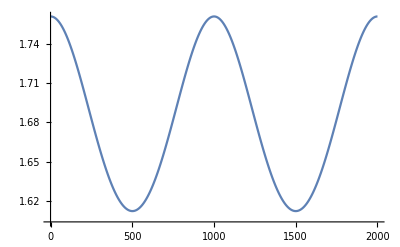

```mathematica
ListLinePlot [Values @ First @ FindRoot [Parameters["H[x,p,m]"][#,-2/(m^(1-.5)),m],{m,1}]& /@Table[i,{i,0,1,1/2000}]]
```

j from critical cong. use this in the rhs. maybe some jt is now defined and changes the value of that initial j. so, if we use the association to update the solution rules, we will alwas retrieve the most up - to - date values.